```mathematica
(*Just some ploting options*)
Needs["ErrorBarPlots`"]
PlotOptions1={FrameTicks->{Automatic,Automatic,None,None},Frame->True,FrameStyle->Directive[Thick,Dashing[2],Black],FrameTicksStyle->Directive[30,Black],LabelStyle->{25,FontFamily->"Helvetica",Black},ImageSize->1200,PlotStyle->{Black,Thick},Axes->False};
```

```mathematica
(*This is just to monitor the parallel code*)
kernels=ParallelTable[$KernelID->i,{i,$KernelCount}];
SetSharedVariable[kernels];SetSharedVariable[currentNumber]
currentNumber=ConstantArray[0,Length@kernels];
```

(*the meaning  of colummns in the maleset and femaleset*)
1. seniority, 2. number of references, 3. number of authors, 4. year of publication, 5. publication, 6. field,7. region -> number of citations

```mathematica
SetDirectory["/export/data1/caplarn/Documents/Gender/Web"];
Get["maleset"];
Get["femaleset"];
yFemaleP=Flatten[Import["yFemaleP.csv"]];
```

```mathematica
(*Messages such as "Message::name: "Message name Part::partd is not of the form symbol::name or symbol::name::language."" are no problem*)
Off[Part::partd];ParallelEvaluate[Off[Part::partd]];Off[Part::partd];ParallelEvaluate[Off[Part::partw]];
PrintTemporary@Dynamic[currentNumber];
PositionsOfYears=ParallelTable[currentNumber[[$KernelID/.kernels]]=y;Flatten[Position[femaleset,_?(#[[1,4]]==y&)]],{y,1959,2015}];
```

Message::name: Message name Part::partd is not of the form symbol::name or symbol::name::language.

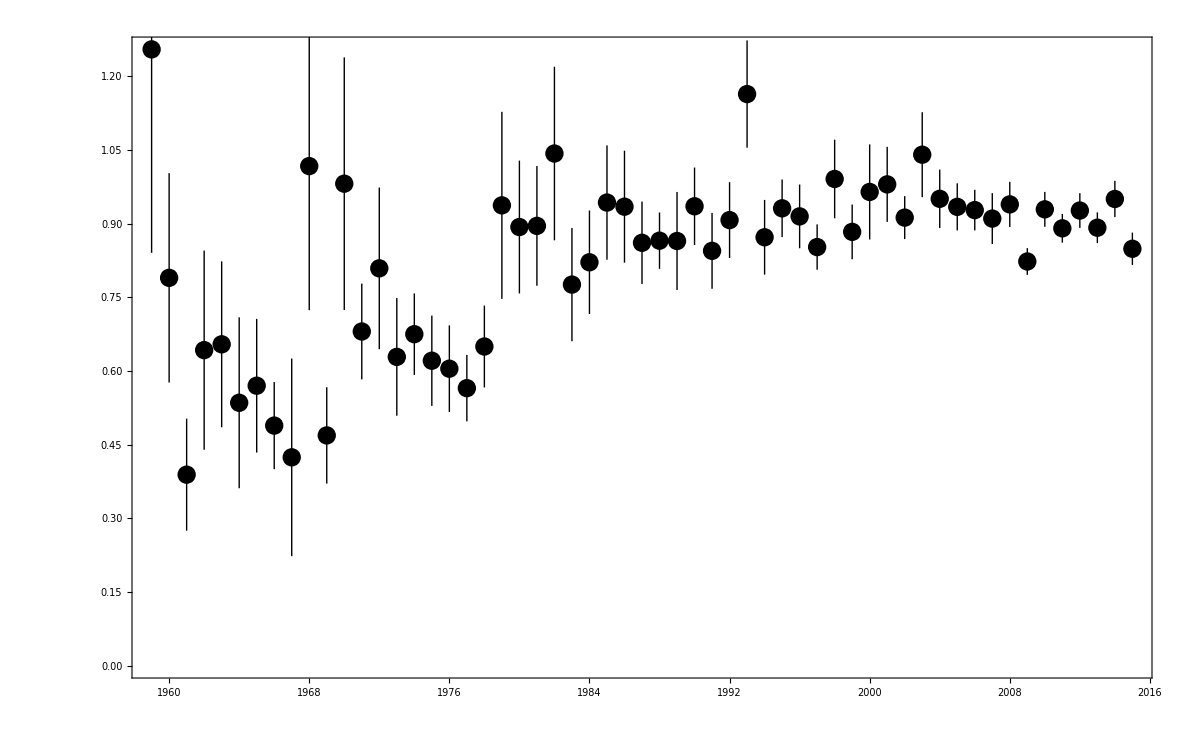

```mathematica
ErrorListPlot[FemFemResult=Table[help=Table[Mean[RandomChoice[femaleset[[PositionsOfYears[[y]]]][[All,2]],Length[PositionsOfYears[[y]]]]],{j,100}];
helpP=Table[Mean[RandomChoice[yFemaleP[[PositionsOfYears[[y]]]],Length[PositionsOfYears[[y]]]]],{j,100}];
{{y+1958,Mean[help/helpP]},ErrorBar[StandardDeviation[help/helpP]]},{y,1,57}],PlotOptions1]
```